InterpolatingFunction[{{200.,1600.},{5.,20.}},<>]

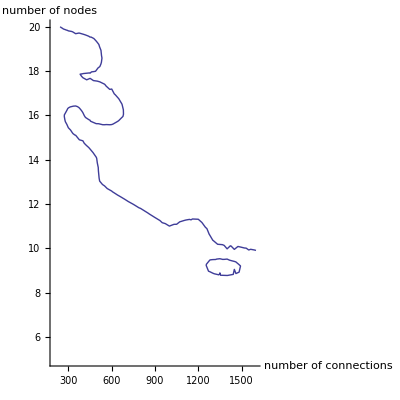

-Graphics3D-

InterpolatingFunction[]

```mathematica
SetDirectory[NotebookDirectory[]];
data:=Import["benchfile-5to20-2cores.txt", "CSV"]
par:=data[[All, {1,2,4}]]
seq:=data[[All, {1,2,3}]]
Interpolation[par]
ppar =ListPlot3D[par,InterpolationOrder->1,Mesh->None,ColorFunction->Function[{x,y,z},Hue[z]]];
spar=ListPlot3D[seq,InterpolationOrder->1,Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[z,z,z]]];
cplot=ContourPlot[Interpolation[par][x,y]==Interpolation[seq][x,y]//Evaluate,{x,200,1600},{y,5,20},Axes->True,Frame->False,AxesLabel->{"number of connections","number of nodes"},PerformanceGoal->Quality]
Show[ppar,spar,PlotRange->All,Axes->True,PlotLabel->"Solver Runtime",AxesLabel->{"number of nodes","number of connections"}]
```